A Computational Model for Invasion Sports

Willem nielsen

Soccer, basketball and hockey are widely practiced and spectated. Understanding the dynamics of these sports is important for players and coaches at all levels. There are obvious similarities between these so-called “Invasion Sports” and I was curious if I could capture them in a computational model.

### It’s All About Space

My idea here is that in any invasion sport, the attackers are trying arrange themselves to maximize the number of different ways they can score. For example, in basketball, a pick and roll creates a dual-threat of the dribbler driving to the basket or passing to the roller for a layup. In soccer you often see one player making a run which frees up another player.

Put more generally, the attackers are trying to maximize the number of dangerous places the ball can be in a given time frame. This means the defenders cannot prevent all the threats.

What’s interesting is if you encode this simple strategy into a computational model, you get realistic play:

The attackers are trying to reach the red endzone without letting the defenders touch the ball. In this case the defense is overaggressive going for a steal. The offense then takes advantage by cutting straight to the endzone with a series of passes. Now, what’s cool about this model is we can scale it up and down and see how things change.

Let’s start with the most basic game and see what happens as we increase the number of players.

2v3 Game:

Here the attackers weren’t able to progress all the way to the endzone, eventually giving up a steal. Again, the attackers are trying to maximize threatening ball positions, so less players means less potential passes. Let’s add an attacker.

3v3 Game:

The attackers were able to leverage the extra player to score a touchdown. Let’s add a defender now.

3v4 Game:

The extra defender led to a steal. So we’re seeing examples of how the model scales, but can we make this more precise? One approach is to simply track the ball, here’s a path of the ball from the previous game:

-Graphics-

Now let’s track the ball over many games. Let’s increase the court length and game length to get a sense for the rate of progression. This time let’s increase the arm strength and see how that affects the attackers’ success.

2v3:

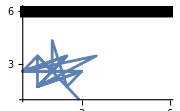
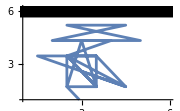
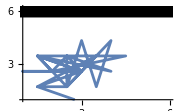
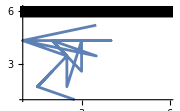
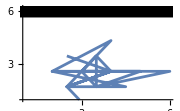
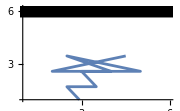
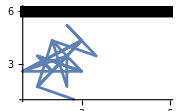
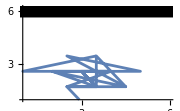

2v3 with higher arm strength:

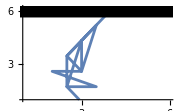
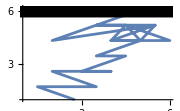
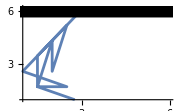
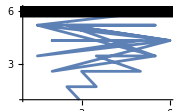
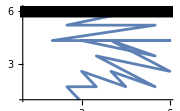
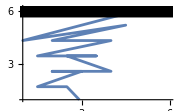
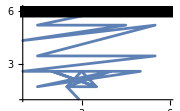
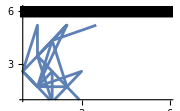

So you can see they are throwing longer passes and progressing further, scoring 9/10 times.

### Squeezing Dimensions

Another surprising discovery was that these scaling laws of arm strength can be captured in 1 dimension. Here we have a passer (black), an attacker (blue) and a defender (red). The ball moves like a knight in chess, “flying above” the players. Based on the position of the defender, the attackers will either go for a short or long pass.

The defender gives ample space forcing the offense to go for a short pass:

The defender gets too close allowing the attacker to run by him for a long pass:

Note that the attacker positions himself right in the place where he can catch a long or short pass. If he lines up too far away, he won’t have the long pass option and the defender can then simply cut off the short pass. If he lines up too close, he won’t maximize the yardage gain.

We can then chain these passes together and add a touch of randomness to get a sense for the progression of the attacking team:

5 consecutive passes

So the attackers made it about a third of the way up the field. Let’s see what happens if we double the arm strength.

They made it about 2/3 of the way this time. One subtlety here is that not only is the attackers rate of progression proportional to arm strength, but also the dispersion of the players. By allowing long passes, you incentivize off-ball attackers to move further away from the ball.

This used to drive me nuts while coaching youth players. Because they aren’t strong or skilled enough to throw long passes, the defense is incentivized to play hyper-aggressively, developing bad habits, and the offense is incentivized to crowd the ball. You address this by creating advantages for the attackers like extra players, or being the point guard yourself.

### Looking Off The Court

For me, It’s been thoroughly enjoyable to distill effects that I’ve observed in practice into the simplest possible computational form. I have much more that I wasn’t quite ready to show here, like an algorithm that works for 10+ players and a much larger court, or a graph for the 1D game that allows you to see the precise optimal positioning for attacker and defender. I’m also excited to look outside the world of sports and model other invasion dynamics like pack hunting and war. My time at the Wolfram Summer School allowed me to build a strong foundation and I feel like this is just the beginning... Thank you for reading.

## 2D Model Code

### Initialization

```mathematica
getHad[turn_]:= If[turn == "α", homeAwayDistance, -homeAwayDistance]
```

```mathematica
getPoint[center_,angle_,radius_]:=center+radius*AngleVector[angle]
getAwayPoints[homePoints_, homeAwayDistance_:1/10]:= Map[{#[[1]],#[[2]] + homeAwayDistance}&, homePoints, {2}]
getRecPoints[point_, size_]:={getPoint[point, 225Degree, size], getPoint[point, 45Degree, size]}
getTriPoints[point_, size_]:=
{getPoint[point, 88Degree, size - 1/12],getPoint[point, 210 Degree, size], getPoint[point, 330Degree, size ]}
```

```mathematica
getPlayerLoc[team_, i_]:= If[team == "home", homePlayers[[i]], awayPlayers[[i]]]
getHomePlayers[startCol_:1, spacing_:1, nPlayers_:3, row_:1]:= Module[{hidxs},
hidxs = NestList[#+spacing&, startCol, nPlayers - 1];
homeLocs[[row, hidxs]]
]

getAwayPlayers[startCol_:1, spacing_:1, nPlayers_:3, row_:-1]:=Module[{idxs},
idxs = NestList[#+spacing&, startCol, nPlayers - 1];
awayLocs[[row, idxs]]
]
```

```mathematica
initializePlayers[nHome_:3, nAway_:3,hspacing_:ballSpeed, aspacing_:ballSpeed, hStartCol_:1, aStartCol_:1, homeStartRow_:1, awayStartRow_:-1]:=
Module[{hidxs, aidxs}, 
hidxs = NestList[#+hspacing&, hStartCol, nHome - 1];
aidxs = NestList[#+aspacing&, aStartCol, nAway - 1];
{homeLocs[[homeStartRow, hidxs]], awayLocs[[awayStartRow, aidxs]]}
]
```

### Visualization

```mathematica
Options[showGame] = {highlightPoints->{}};
showGame[{homePlayers_, awayPlayers_ , ballLoc_, turn_, guardedCount_, res_}, OptionsPattern[{Graphics, showPlay, showGame}]]:=Module[{hpRecs, apTris, allShapes, dribbler,ball, g},
	hpRecs = Rectangle@@getRecPoints[#, playerSize]&/@ homePlayers;
	apTris = N/@Polygon@getTriPoints[#,playerSize]&/@ awayPlayers;
	ball = Disk[ballLoc, ballSize];
	g = Graphics[{FaceForm@White,background, FaceForm@LightRed, endzone, FaceForm@Gray, Point@N@Flatten[OptionValue[points], 1], FaceForm@Blue, hpRecs,FaceForm@Red,apTris, Green, ball,
	Red, Point@OptionValue[highlightPoints]}, ImageSize->OptionValue[ImageSize]]
(*	If[OptionValue[showEvaluation], Column[g, getEvaluation[{homePlayers, awayPlayers, ballLoc, turn, guardedCount, res}]]]*)
]
```

#### Show one move

```mathematica
getObjectMovementFrames[start_, end_, frames_:20]:= Subdivide[start, end,frames]

getMoveFrames[gameStateStart_, gameStateEnd_, frameRate_:10]:= Module[{go1, go2, gf1, gf2, turn, gc, hpl, apl, objectFrames, gameStatesFlat, 
gameObjectFrames, gameStates, res}, 
  go1 = gameStateStart[[;;2]];
  go2 = gameStateEnd[[;;2]];
  gf1 = Append[Flatten[go1, 1], gameStateStart[[3]]];
  gf2 = Append[Flatten[go2,1], gameStateEnd[[3]]];
  turn = gameStateEnd[[4]]; gc = gameStateEnd[[5]];res = gameStateEnd[[6]];
  objectFrames = MapThread[getObjectMovementFrames[#1, #2, frameRate]&, {gf1, gf2}];
  gameStatesFlat = Transpose[objectFrames];
  hpl = Length@homePlayers; apl = Length@awayPlayers;
  gameObjectFrames = {#[[;;hpl]], #[[hpl+1;;hpl+apl]],#[[hpl+apl+1]]}&/@ gameStatesFlat;
  gameStates = Join[#, {turn, gc, res}]& /@ gameObjectFrames
  ]

getMoveFrameGraphics[gameStateStart_, gameStateEnd_, frameRate_:10]:= Module[{moveFrames}, 
  moveFrames = getMoveFrames[gameStateStart, gameStateEnd, frameRate];
  showGame/@ moveFrames
  ]

showMove[gameStateStart_, gameStateEnd_, frameRate_:20]:= Module[{graphicsFrames}, 
  graphicsFrames = getMoveFrameGraphics[gameStateStart, gameStateEnd, frameRate];
  ListAnimate[graphicsFrames, DefaultDuration->1, AnimationRepetitions->1]
 ]
```

#### Show entire play

```mathematica
alignFrames[attackers_, defenders_, delay_:5]:=Module[{},
defendersDelayed = Join[Table[First@defenders, delay], defenders];
lengthDiff = Length@attackers - Length@defendersDelayed;
Which[
lengthDiff == 0, {attackers, defendersDelayed},
Positive[lengthDiff], {attackers, Join[defendersDelayed, Table[Last@defendersDelayed, lengthDiff]]},
Negative[lengthDiff], {Join[attackers, Table[Last@attackers, -1*lengthDiff]], defendersDelayed}
]]

mergeGames[attackerGameState_,defenderGameState_]:=  
{attackerGameState[[1]], defenderGameState[[2]], attackerGameState[[3]], attackerGameState[[4]], defenderGameState[[5]], defenderGameState[[6]]}
```

```mathematica
getPlayGraphicFrames[moves_, op___]:= Module[{attackingTeam, defendingTeam, movePairs, attackingMovePairs, defendingMovePairs, attackingFrames, defendingFrames, allFrames, mergedFrames,
graphics}, 
attackingTeam =moves[[1, 4]]; defendingTeam = flip@attackingTeam;
movePairs = Partition[moves, 2, 1];
attackingMovePairs  = Select[movePairs, #[[2, 4]] == defendingTeam&];
defendingMovePairs = Select[movePairs, #[[2, 4]] == attackingTeam&];
attackingFrames =  Flatten[getMoveFrames@@@ attackingMovePairs, 1];
defendingFrames = Flatten[getMoveFrames@@@ defendingMovePairs, 1];
allFrames =alignFrames[attackingFrames, defendingFrames];

mergedFrames = MapThread[mergeGames[#1, #2]&, allFrames];
graphics = showGame[#, op]& /@ mergedFrames
]
```

```mathematica
Options[showPlay] = {duration->5, points->{}};
showPlay[moves_,op___]:= Module[{frames}, 
frames = getPlayGraphicFrames[moves, op];
ListAnimate[frames, DefaultDuration->5, AnimationRepetitions->1]
]
```

```mathematica
getVideo[play_,frameRate_:15, op___]:= Module[{frames}, 
frames = getPlayGraphicFrames[play];
FrameListVideo[frames, FrameRate->frameRate]
]
```

#### Other

```mathematica
overlayAttackingMove[move_, gameState_, op___]:= showGame[ReplacePart[gameState, {1->Most[move], 3->Last[move]}] , op]
overlayDefendingMove[move_, gameState_]:= showGame[ReplacePart[gameState, 2->move]]
```

```mathematica
showAttackingMove[{players__, ballLoc_}, team_, OptionsPattern[{showPlay, showGame}]]:=Module[{hpRecs, apTris, allShapes, dribbler},
playerShapes = If[team == "home",  Rectangle@@getRecPoints[#, playerSize]&/@ {players}, 
 N@Polygon@getTriPoints[#,playerSize]&/@ awayPlayers];
ball = Disk[ballLoc, ballSize];
color = If[team== "home", Blue, Red];
Graphics[{FaceForm@White,background, FaceForm@Gray, Point@N@OptionValue[points], FaceForm@color, playerShapes, Green, ball,
	Red, Point@OptionValue[highlightPoints]}]]
```

```mathematica
showDefensiveMove[players_, team_, OptionsPattern[{showPlay, showGame}]]:=Module[{hpRecs, apTris, allShapes, dribbler},
playerShapes = If[team == "home",  Rectangle@@getRecPoints[#, playerSize]&/@ players, 
 N/@Polygon@getTriPoints[#,playerSize]&/@ players];
color = If[team== "home", Blue, Red];
Graphics[{FaceForm@White,background, FaceForm@Gray, Point@N@OptionValue[points], FaceForm@color, playerShapes,
	Red, Point@OptionValue[highlightPoints]}]]
```

### Game Logic

#### Booleans

```mathematica
guardedQ[{homePlayers_, awayPlayers_ , ballLoc_, turn_, guardedCount_, res_}]:=
  MemberQ[awayPlayers, {ballLoc[[1]], ballLoc[[2]]+1/10}] || MemberQ[homePlayers, {ballLoc[[1]], ballLoc[[2]]-1/10}]

flip[turn_]:= Replace[turn, {"α"->"β","β"->"α"}]

  getAttackerTurn[{homePlayers_, awayPlayers_ , ballLoc_, turn_, gc_, res_}] := 
    Which[
	MemberQ[homePlayers, ballLoc], "α",
	MemberQ[awayPlayers, ballLoc], "β",
	True, "α"]
```

```mathematica
turnoverQ[{homePlayers_, awayPlayers_ , {ballX_, ballY_}, turn_, guardedCount_, res_}]:= 
Module[{maySteal, awaySteal, homeSteal},
maySteal = guardedCount == stealDifficulty;
awaySteal = MemberQ[awayPlayers, {ballX,ballY + homeAwayDistance}];
homeSteal =MemberQ[homePlayers, {ballX,ballY - homeAwayDistance}];
If[(maySteal && awaySteal) || (maySteal && homeSteal), True, False]
]
```

```mathematica
gameOverQ[gameState_]:=Module[{}, 
touchdownQ[gameState]|| interceptionQ[gameState] || turnoverQ[gameState]
]
```

```mathematica
interceptionQ[defenders_, {ballX_, ballY_}, turn_:"α"]:=Module[{},
had = getHad[turn];
MemberQ[defenders, {ballX,ballY + had}]
]
```

```mathematica
touchdownQ[{ballX_, ballY_}, turn_:"α"]:= Module[{}, 
ez = If[turn == "α", homeEndZoneY, awayEndZoneY];
ballY == ez
]
```

```mathematica
attackerTurnQ[gameState_]:= Module[{},
{hps, aps, ballLoc, turn ,gs, res} = gameState;
(MemberQ[hps, ballLoc]&& turn == "α") || (MemberQ[aps, ballLoc]&& turn == "β" )
]
```

#### Evaluating State

```mathematica
getEZ[turn_]:= If[turn == "α", {homeEndZoneY, awayEndZoneY},{awayEndZoneY, homeEndZoneY} ]
```

```mathematica
getWeightedDistancesToBall[players_, ball_]:= Module[{}, 
(*weight =If[ball == ez,100, ball[[2]]];  *)
EuclideanDistance[#, ball]*ball[[2]]&/@ players 
]
```

```mathematica
evaluateAttackingState[move_, gameState_]:=Module[{},
turn = getAttackerTurn[gameState]; defenders = getDefenders[gameState];had = getHad[turn];
ballLoc = Last[move]; attackers = Most[move];
{hez, aez} = getEZ[turn];
Which[
interceptionQ[defenders, ballLoc], ballLoc[[2]]+had - hez,
	(*td*)
	MemberQ[attackers,ballLoc]&&ballLoc[[2]] == hez, 100,
(*The further up the field the better*)
MemberQ[attackers,ballLoc], ballLoc[[2]] - aez+2/10,
	True, 0
]]
```

```mathematica
getClosest[{defense_, res_}, ballLoc_]:= Module[{}, 
ballDistances = getWeightedDistancesToBall[defense, ballLoc];
minIdx = First@PositionSmallest[ballDistances];
min = Min[ballDistances];
out = {Delete[defense, minIdx], min}]
```

```mathematica
evaluateDefensiveState[defense_, ballLocs_] := Module[{},
minList = FoldList[getClosest,{defense,0}, ballLocs];
mins = minList[[2;;, 2]];
sumMinDistances = Total[mins]
]
```

evaluate state is still a work in progress

```mathematica
evaluateState[gameState_]:= Module[{}, 
{homePlayers, awayPlayers , ballLoc, turn, guardedCount, result} = gameState;
attackers = getAttackers[gameState];
defenders = getDefenders[gameState];
amoves = filterAttackingMoves[getAttackerMoves[gameState], gameState]; 
amBest = TakeLargestBy[amoves, evaluateAttackingState[#,gameState]&, UpTo[3]];
If[attackerTurnQ[gameState], evaluateAttackingState[Append[attackers, ballLoc], gameState],
  evaluateDefensiveState[defenders, Union@amBest[[All, 4]]]]
]
```

#### Getting Moves

```mathematica
getMovesBounded[currentPoint_, speed_:playerSpeed]:=Module[{allPoints},
  allPoints = Map[getPoint[currentPoint, #, speed]&, directions];
  Select[allPoints, RegionMember[gamePoly, #]&]
]
getMovesBoundedStatic[currentPoint_, speed_:1]:=Module[{allPoints},
  allPoints = Append[Map[getPoint[currentPoint, #, speed]&, directions], currentPoint];
  Select[allPoints, RegionMember[gamePoly, #]&]
]
getMovesBoundedExcept[players_, pg_, moveFunc_:getMovesBounded]:= Insert[(moveFunc/@Delete[players, pg]), {players[[pg]]}, pg]
```

```mathematica
getDefenders[{homePlayers_, awayPlayers_ , ballLoc_, turn_, guardedCount_, res_}]:= If[MemberQ[homePlayers, ballLoc], awayPlayers, homePlayers]
```

```mathematica
getAttackers[{homePlayers_, awayPlayers_ , ballLoc_, turn_, gc_, res_}]:= If[MemberQ[homePlayers, ballLoc], homePlayers, awayPlayers]
```

```mathematica
getDefenderMoves[currentLocs_]:=Tuples[(getMovesBoundedStatic/@ currentLocs)]
```

```mathematica
getAttackerMoves[gameState_, rule_:"static"]:=Module[{},
 {homePlayers, awayPlayers , ballLoc, t, guardedCount, res}  = gameState;
attackers = getAttackers[gameState]; 
turn = getAttackerTurn[gameState];
pg = getpg[attackers, ballLoc];
playerMoves = If[rule == "static",getMovesBoundedExcept[attackers, pg],getMovesBounded/@ attackers];
ballMoves= getBallMoves[ballLoc, turn];
allMoves = Append[playerMoves, ballMoves];
Tuples[allMoves]
]
```

```mathematica
getAttackerGameState[move_, gameState_]:=Module[{},
 {h, a, ballLoc, t, gc, res}  = gameState;
defenders = getDefenders[gameState];
turn = getAttackerTurn[gameState];
result = Which[
interceptionQ[defenders, Last[move]], -100,
touchdownQ[Last[move]],100,
True, 0
];
replaceIdx = If[turn == "α", 1, 2];
ReplacePart[gameState, {replaceIdx->Most[move], 3->Last[move], 4->flip@turn, 6->result}]
]
```

```mathematica
getDefenderGameState[move_, {homePlayers_, awayPlayers_ , ballLoc_, turn_, guardedCount_, res_} ]:=Module[{},
replaceIdx = If[turn == "α", 1, 2];
ReplacePart[{homePlayers, awayPlayers , ballLoc, flip@turn, guardedCount, res}, replaceIdx->move]
]
```

```mathematica
getBallMoves[ballLoc_, turn_:"α"]:= Module[{allPoints},
  If[turn == "α", Select[Flatten[homeLocs, 1], EuclideanDistance[ballLoc, #]<= ballSpeed &], 
  Select[Flatten[awayLocs, 1], EuclideanDistance[ballLoc, #]<= ballSpeed &]]
]
```

```mathematica
turnover[{homePlayers_, awayPlayers_ , {ballX_, ballY_}, turn_, guardedCount_, res_}]:= 
Module[{maySteal, awayStealY, homeStealY, awaySteal, homeSteal},
maySteal = guardedCount == stealDifficulty;
awayStealY = ballY+homeAwayDistance;
homeStealY =  ballY-homeAwayDistance;
awaySteal = MemberQ[awayPlayers, {ballX,awayStealY}];
homeSteal =MemberQ[homePlayers, {ballX,homeStealY}];
Which[
maySteal&&awaySteal,  {homePlayers, awayPlayers, {ballX, awayStealY}, "β", -1},
maySteal&&homeSteal,  {homePlayers, awayPlayers, {ballX, homeStealY}, "α", -1},
awaySteal||homeSteal,  {homePlayers, awayPlayers, {ballX, ballY}, turn, guardedCount+1},
True, {homePlayers, awayPlayers , {ballX, ballY}, turn, 0}
]]
```

#### Choosing Moves

```mathematica
removeOverlaps[moveComs_]:=  Cases[moveComs,{players__, ball_}/;DuplicateFreeQ[{players}]];
removeIncompletePasses[moveComs_]:= Cases[moveComs,{players__, ball_}/;MemberQ[{players}, ball]];
removeTravelling[moveComs_, ballLoc_, pg_]:= DeleteCases[moveComs,{players__, ball_}/;(ball!= ballLoc)&& {players}[[pg]] == ball]
```

```mathematica
getpg[attackers_, ballLoc_]:= First@FirstPosition[attackers, ballLoc]
```

```mathematica
filterDefensiveMoves[moveComs_]:= removeOverlaps@DeleteDuplicatesBy[moveComs, Sort]
```

```mathematica
filterAttackingMoves[moveComs_, gameState_, OptionsPattern[getBestMove]]:= Module[{},
(*If duplicates by is ball it only takes one instance of each ball location otherwise 
it removes all cases where players are in same formation*)
attackers = getAttackers[gameState]; ballLoc = gameState[[3]]; pg = getpg[attackers, ballLoc];
dupsBy = If[OptionValue[duplicatesBy] == "ball", Last, Sort];
filters = {RandomChoice/@ GatherBy[#, dupsBy]&};
If[!OptionValue[overlaps], AppendTo[filters, removeOverlaps]];
If[!OptionValue[incompletePasses], AppendTo[filters, removeIncompletePasses]];
If[OptionValue[travels], AppendTo[filters, removeTravelling[#, ballLoc, pg]&]];
(Composition@@filters)[moveComs]
]
```

```mathematica
getBestDefensiveMoves[defenders_, ballLocs_, n_:1]:= Module[{},
defenderPositionsList = filterDefensiveMoves@getDefenderMoves[defenders];
bestPos = TakeSmallestBy[defenderPositionsList, evaluateDefensiveState[#, ballLocs]&, UpTo[n]]
]
```

```mathematica
getBestAttackingMoves[gameState_, n_:3]:=  Module[{},
moves = getAttackerMoves[gameState];
filtered = filterAttackingMoves[moves,gameState];
best =  TakeLargestBy[filtered, evaluateAttackingState[#,gameState]&, UpTo[n]]
]
```

```mathematica
Options[getBestMove] = {overlaps->False, incompletePasses->False,travels->True, shorten->True, duplicatesBy->"ball"};
getBestMove[gameState_, op___]:=  Module[{ballLoc},
{homePlayers, awayPlayers , ballLoc, turn, guardedCount, result} = gameState;
If[result!=0, Return[{}],
{players, oppPlayers}=  If[turn == "α", {homePlayers, awayPlayers},{awayPlayers, homePlayers}] ;
{attackingTeam, attackerTurn} = If[MemberQ[homePlayers, ballLoc], {"home", "α"},{"away", "β"}] ;
pos = MemberQ[players, ballLoc];
{attackers, defenders} ={getAttackers[gameState], getDefenders[gameState]};
pg = getpg[attackers, ballLoc];
amoves = getAttackerMoves[gameState];
amovesFiltered = filterAttackingMoves[amoves,gameState, FilterRules[op]];
bestAttackingMoves=  TakeLargestBy[amovesFiltered, evaluateAttackingState[#,gameState]&, UpTo[Length@defenders]];
If[pos, 
ags = getAttackerGameState[RandomChoice@bestAttackingMoves,gameState],
bestDefensiveMoves = getBestDefensiveMoves[defenders, Union@bestAttackingMoves[[All, -1]], 3]; 
getDefenderGameState[RandomChoice@bestDefensiveMoves, gameState]
]]]
```

```mathematica
getBestMoveFast[gameState_, op___]:=   Module[{ballLoc},
{homePlayers, awayPlayers , ballLoc, turn, guardedCount, result} = gameState;
If[result!=0, Return[{}],
{players, oppPlayers}=  If[turn == "α", {homePlayers, awayPlayers},{awayPlayers, homePlayers}] ;
pos = MemberQ[players, ballLoc];
{attackers, defenders} ={getAttackers[gameState], getDefenders[gameState]};
bestAttackingMoves=  getBestAttackingMoves[gameState, 5];
If[pos, 
ags = getAttackerGameState[RandomChoice[{2/3, 1/3}->Take[bestAttackingMoves, 2]],gameState],
bls = bestAttackingMoves[[All, -1]];
bdm = moveDefenders[defenders, Take[bls, UpTo[Length@defenders]]]; 
getDefenderGameState[bdm, gameState]
]]]
```

```mathematica
getPlay[initialGameState_,n_:10, iterator_:getBestMoveFast]:= 
Most@NestWhileList[iterator, initialGameState, # != {}&,1, n];
```

```mathematica
getNearest[{defense_, res_}, ballLoc_]:= Module[{}, 
near = First@Nearest[defense, ballLoc, 1];
nd = DeleteElements[defense, 1->{near}];
out = {nd, near}
]

getMoveRule[taken_, {player_,point_}]:= Module[{notgone, op, angle, ned, np=-1},
If[EuclideanDistance[player, point]<= homeAwayDistance,  Sow[player->player];Return@Append[taken, player],
notgone = directions;
op = getPoint[point, 0 ,-1];
angle = PlanarAngle[point->{op, player}];
While[MemberQ[taken, np], 
If[notgone == {}, Sow[player->player];Return@Append[taken, player]];
ned = First@Nearest[notgone, angle, 1];
np =  getPoint[player,ned, playerSpeed];
notgone = DeleteCases[notgone, ned];
];
Sow[player-> np];
Append[taken, np]
]]
moveDefenders[defenders_, ballLocs_]:= Module[{}, 
nearList = FoldList[getNearest, {defenders, 0}, ballLocs];
neartobl = nearList[[2;;, 2]];
nt = Transpose[{neartobl, ballLocs}];
mrs = Reap[FoldList[getMoveRule, {-1}, nt]];
reaped = mrs[[2, 1]];
newd = ReplaceAll[defenders, reaped]
]
```

### Court

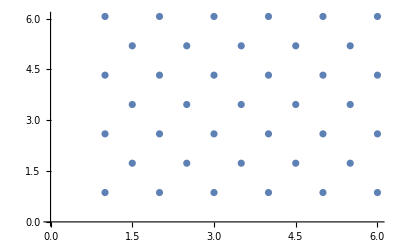

```mathematica
courtWidth = 5;
courtLength =6;
endzone = Rectangle[{1/2, (courtLength+1/2)(Sqrt[3]/2)}, {courtWidth+3/2, (courtLength+3/2)(Sqrt[3]/2)}];
directions = NestList[#+60Degree&, 0Degree, 6];
bottomLeftPoint = {1, 1};
background = Rectangle[bottomLeftPoint - {1, 1/2}, {courtWidth+2, courtLength+1}];
p = getPoint[bottomLeftPoint, 60Degree, 1]; 
{shortRowOffset, rowDiff} =p - bottomLeftPoint;
longRows = Table[NestList[getPoint[#, 0, 1]&, 
{bottomLeftPoint[[1]], (i - bottomLeftPoint[[2]]+ 1)*rowDiff},
 courtWidth], 
{i, bottomLeftPoint[[2]], courtLength+1, 2}];
shortRows = Table[NestList[getPoint[#, 0, 1]&, {p[[1]], (i - p[[2]]+2)*rowDiff}, courtWidth-1], {i, p[[2]], courtLength+1, 2}];
homeLocs = Riffle[longRows, shortRows];
homeAwayDistance = 1/10;
awayLocs = getAwayPoints[homeLocs, homeAwayDistance];
homeEndZoneY = homeLocs[[-1, 1, 2]];
awayEndZoneY = awayLocs[[1,1, 2]];
allLocs = Flatten[Join[homeLocs, awayLocs], 1];
gamePoly = BoundingRegion[allLocs, "MinConvexPolygon"];
ListPlot[Tooltip[#, #]&/@ Flatten[homeLocs, 1]]
```

### Object Parameters

```mathematica
playerSize = 1/5;
ballSize = 1/8;
playerSpeed = 1;
ballSpeed= 5;
stealDifficulty = 1;
```

### Constants

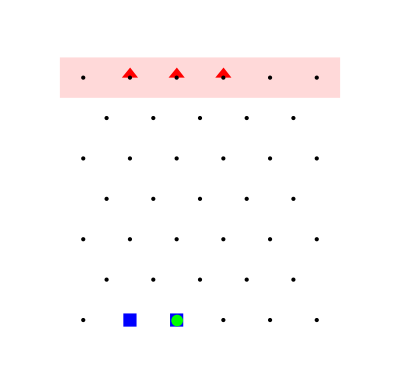

```mathematica
awayPlayers = getAwayPlayers[2, 1, 3];
homePlayers = getHomePlayers[2, 1, 2];
allPlayers = Join[homePlayers, awayPlayers];
turn = "α";
ballStart = 2;
ballLoc = getPlayerLoc["home", ballStart];
initialGuardCount = 0;
initialResult = 0;
initialGameState = {homePlayers, awayPlayers, ballLoc, turn, initialGuardCount, initialResult};
showGame[initialGameState, points->homeLocs]
```

### Play Game

```mathematica
play = getPlay[initialGameState, 30];
```

Nearest::mepcmp: Internal extra precision limit $MaxExtraPrecision reached for some distance comparisons.  These distances were taken as equal even though strict equality was not verified.  Increasing the value of $MaxExtraPrecision may resolve the uncertainty.

```mathematica
sp = showPlay[play,ImageSize->400]
```

## 1D Model Code

### Visualizations

```mathematica
showRoute[route_]:= Module[{frames},
ListAnimate[getPlot/@ route, DefaultDuration->2, AnimationRepetitions->1]
]
```

```mathematica
getPlot[state_, bstart_]:= showFrame@getFrame[state, bstart]
```

```mathematica
showFrame[frame_]:= ArrayPlot[frame, ColorRules->colorRules,AspectRatio->1/12, ImageSize->400]
```

```mathematica
getFrame[{attackers_, defenders_, ball_}, bstart_]:= Module[{anum, dnum, aparts, dparts, pparts}, 
{anum, dnum } = If[attackers == defenders, {5, 5}, {1, 2}];
aparts = {#, attackers}->anum&/@ Range[2, 5];
dparts = {#, defenders}->dnum&/@ Range[2, 5];
pparts =  {#, bstart}->4&/@ Range[2, 5];
ReplacePart[gameArray, Join[aparts, dparts,pparts ,{ {1, ball}->3}]
]]
```

```mathematica
showRoute[route_, bstart_]:= getPlot[#, bstart]&/@ route
```

### Game Logic

```mathematica
canGoShortQ[defender_]:=shortPass+(shortPass - ballStart)/ballSpeed - reactionTime < defender
```

```mathematica
canGoLongQ[astart_, dstart_]:= dstart - astart < reactionTime
```

```mathematica
roundDownToOdd[n_]:=Module[{floor},floor=Floor[n];
If[OddQ[floor],floor,floor-1]]
```

```mathematica
getPass[features_]:= Module[{dest, amoves, bmoves, await, bwait, pass},
dest = features["passLoc"];
amoves = Range[features["astart"],  dest, If[dest>features["astart"], playerSpeed,-playerSpeed]];
bmoves = Range[features["bstart"], dest, ballSpeed];
await = If[Length@bmoves > Length@amoves,PadRight[amoves, Length@bmoves, Last[amoves]], amoves];
bwait = If[Length@bmoves < Length@amoves, PadRight[bmoves, Length@amoves,Last[bmoves]], bmoves];
pass = Transpose[{await, bwait}]
]
```

```mathematica
guard[bstart_, bdest_, dstart_]:= Module[{move, delay, wait},
move = Range[dstart, bdest, If[bdest>dstart, playerSpeed,-playerSpeed]];
delay = Join[Table[dstart, reactionTime],move];
wait = PadRight[delay,  (bdest - bstart) / ballSpeed+1, Last[delay]]
]
```

```mathematica
getFeatures[ballStart_]:= Module[{lpass, astart, dvariance, dstart, spass, longQ, passLoc}, 
lpass = armStrength+ballStart;
astart= Floor[lpass  - (armStrength/ballSpeed)playerSpeed];
dvariance = RandomChoice[{1/3, 1/3, 1/3}->{-1, 0, 3}];
dstart =astart+reactionTime+dvariance;
spass = roundDownToOdd[((dstart+reactionTime-1)ballSpeed+ballStart)/(ballSpeed+1)];
longQ = canGoLongQ[astart, dstart];
passLoc = If[longQ,lpass, spass];
<|"bstart"->ballStart,"passLoc"->passLoc, "astart"->astart, "dstart"->dstart|>
]
```

```mathematica
sowRoute[ballStart_]:=Module[{features, attacker, defender, ball,pass, dlocs, rlocs}, 
features = getFeatures[ballStart];
pass =getPass[features];
dlocs = guard[ballStart, features["passLoc"], features["dstart"]];
rlocs = MapThread[Insert[#1, #2, 2]&, {pass, dlocs}];
Sow[rlocs, "route"]; Sow[ballStart, "bstart"];pass[[-1, 2]]
]
```

```mathematica
getRouteChain[n_:10]:= Module[{reaped, routes, bstarts, plots}, 
reaped = Reap[Nest[sowRoute, 1, n], {"route", "bstart"}];
routes = reaped[[2, 1, 1]];
bstarts = reaped[[2, 2, 1]];
plots =  Flatten[MapThread[showRoute[#1, #2]&, {routes, bstarts}], 1]
]
```

### Constants

```mathematica
colorRules = {1->Blue, 2->Red, 3->Green, 4->Black, 5->Purple};
gameArray = ConstantArray[0, {5, 100}];
reactionTime = 2;
playerSpeed = 1;
ballSpeed = 2;
nPlayers = 3;
```

### Parameters

```mathematica
armStrength = 20;
```

### Play Game

```mathematica
frames =  getRouteChain[5];
```

```mathematica
ListAnimate[frames]
```

## Acknowledgments

The Wolfram Summer School was a life-changing experience for me. Thank you to Eric James Parfitt, John McNally, Stephen Wolfram and all the others who made this possible.

## Access the Full Code

Scan or visit wolfr.am/ShortURL.

These are a short URL and a QR code used to condense large blocks of code. They will lead to the Wolfram Community version of your project where the full code can be found. Our publishing team will provide these for you. They can be placed anywhere in your project where we want to condense code for print.

## Cite This Notebook

“A Computational Model for Invasion Sports”
by Willem Nielsen
https://community.wolfram.com/groups/-/m/t/3210765?p_p_auth=mnG1KCWE